# 知識構造化法

2013年度　秋学期、筑波大学　学部3・4年次、5・6限

## 2.データの構造について

### 純関数

```mathematica
f[][3,2]/.{f[]->Function[{x,y},x y]}
```

6

```mathematica
FullForm[f']
```

Derivative[1][f]

```mathematica
FullForm[f'[x]]
```

Derivative[1][f][x]

```mathematica
Derivative[1][x^3][x]
```

(x^3)'[x]

```mathematica
Derivative[1][Function[u,u^3]][x]
```

3 x^2

```mathematica
D[x^3,x]
```

3 x^2

## 4.探索的データ解析

### 正規分布

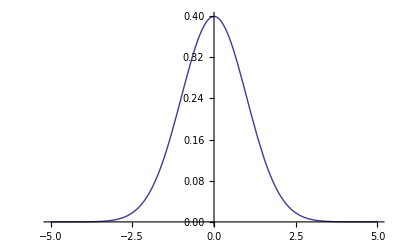

```mathematica
Plot[PDF[NormalDistribution[],m],{m,-5,5}]
```

```mathematica
Integrate[PDF[NormalDistribution[],m],{m,-Infinity,Infinity}]
```

1

## 8.自己組織化マップ

### ニューラルネットワーク

#### ニューロン

加算器

```mathematica
adder[o_List,w_List]:=Tr[w*o]
```

```mathematica
adder[{1,2,3},{a,b,c}]
```

a+2 b+3 c

入出力関数 -シグモイド関数-

```mathematica
SGM[a_,th_]:=1/(1+E^(-a+th))
```

```mathematica
Plot3D[SGM[in,t],{in,-10,10},{t,-5,5},AxesLabel->Automatic]
```

-Graphics3D-

ニューロンの設計

```mathematica
NER[o_List,w_List,iofunc_,th_]:=If[iofunc[adder[o,w],th]>=th,1,0]
```

```mathematica
ner[o_List,w_List,iofunc_,th_]:=iofunc[adder[o,w],th]
```

加算器と入出力関数(iofunc)を組み合わせニューロンを作る。
入出力関数(iofunc)は、いま、シグモイド(0 < SGM < 1)に定義されている。
かつ、ニューロン(NER)は、非線形活性化関数として機能している。
しきい値 th は、iofunc() そのものにも影響するかたちになっている。

設計したニューロンの性質:

入力を{1,1,1}、重みを{10,10,10}とする。

thに1以上を設定すると、ニューロンの出力は、かならず 0。

```mathematica
Table[{NER[{1,1,1},{10,10,10},SGM,th],th},{th,-0.2,1.2,0.1}]//TableForm
```

1 | -0.2
1 | -0.1
1 | 0.
1 | 0.1
1 | 0.2
1 | 0.3
1 | 0.4
1 | 0.5
1 | 0.6
1 | 0.7
1 | 0.8
1 | 0.9
0 | 1.
0 | 1.1
0 | 1.2

```mathematica
Table[{NER[{1,1,1},{-10,-10,-10},SGM,th],th},{th,-0.2,1.2,0.1}]//TableForm
```

1 | -0.2
1 | -0.1
1 | 0.
0 | 0.1
0 | 0.2
0 | 0.3
0 | 0.4
0 | 0.5
0 | 0.6
0 | 0.7
0 | 0.8
0 | 0.9
0 | 1.
0 | 1.1
0 | 1.2

thに0以下を設定すると、ニューロンの出力は、かならず 1。

```mathematica
Table[{NER[{1,1,1},{10,10,10},SGM,th],th},{th,-0.2,1.2,0.1}]//TableForm
```

1 | -0.2
1 | -0.1
1 | 0.
1 | 0.1
1 | 0.2
1 | 0.3
1 | 0.4
1 | 0.5
1 | 0.6
1 | 0.7
1 | 0.8
1 | 0.9
0 | 1.
0 | 1.1
0 | 1.2

```mathematica
Table[{NER[{1,1,1},{-10,-10,-10},SGM,th],th},{th,-0.2,1.2,0.1}]//TableForm
```

1 | -0.2
1 | -0.1
1 | 0.
0 | 0.1
0 | 0.2
0 | 0.3
0 | 0.4
0 | 0.5
0 | 0.6
0 | 0.7
0 | 0.8
0 | 0.9
0 | 1.
0 | 1.1
0 | 1.2

したがって、しきい値は、0から1の範囲で変化させればよい。

次に、入力、重みをすべて負の値とし、thを0 <= th <= 1の間で変化させる。thが0の場合のみ、ニューロンの出力は1。

```mathematica
Table[{NER[{1,1,1},{-1,-1,-1},SGM,th],th},{th,0,1,0.1}]//TableForm
```

1 | 0.
0 | 0.1
0 | 0.2
0 | 0.3
0 | 0.4
0 | 0.5
0 | 0.6
0 | 0.7
0 | 0.8
0 | 0.9
0 | 1.

入力、重みをすべて大きな正の値とし、thを0 <= th <= 1の間で変化させる。thが1に非常に近い場合にのみ、ニューロンの出力は0。

```mathematica
Table[{NER[{1,1,1},{10,10,10},SGM,th],th},{th,0,1,0.1}]//TableForm
```

1 | 0.
1 | 0.1
1 | 0.2
1 | 0.3
1 | 0.4
1 | 0.5
1 | 0.6
1 | 0.7
1 | 0.8
1 | 0.9
0 | 1.

#### 教師あり学習

ニューラルネットワークの簡単な例:

-Graphics-

学習データ: {<入力ベクトル>,<期待される出力>}

```mathematica
ldata1={
{{0,0},0},
{{1,0},0},
{{0,1},0},
{{1,1},1}
}
```

{{{0,0},0},{{1,0},0},{{0,1},0},{{1,1},1}}

```mathematica
TableForm[Map[Flatten[#]&,ldata1],TableHeadings->{Table[n,{n,4}],{"入力１","入力２","出力(期待)"}}]
```

| 入力１ | 入力２ | 出力(期待)
1 | 0 | 0 | 0
2 | 1 | 0 | 0
3 | 0 | 1 | 0
4 | 1 | 1 | 1

重みベクトル、しきい値の初期値

```mathematica
wdata[0]={1.5,-1.0}
```

{1.5,-1.}

```mathematica
thh[0]=0.8
```

0.8

```mathematica
NER[ldata1[[1,1]],wdata[0],SGM,thh[0]]
```

0

```mathematica
NER[ldata1[[2,1]],wdata[0],SGM,thh[0]]
```

0

```mathematica
NER[ldata1[[3,1]],wdata[0],SGM,thh[0]]
```

0

```mathematica
NER[ldata1[[4,1]],wdata[0],SGM,thh[0]]
```

0

上の例では、パターン4のときに期待する値が得られていない。

学習:

重みとしきい値を変化させ、学習をおこなう。

しきい値を小さくすれば、出力は大きくなる。

```mathematica
delta=.
```

```mathematica
thh[0]
```

0.8

```mathematica
ner[ldata1[[4,1]],wdata[0],SGM,thh[0]]
```

0.425557

```mathematica
delta[1]=ner[ldata1[[4,1]],wdata[0],SGM,thh[0]]-thh[0]
```

-0.374443

```mathematica
NER[ldata1[[4,1]],wdata[0],SGM,thh[0]+delta[1]]
```

1

入力に対応する重みを大きくすれば、出力は大きくなる。

```mathematica
wdata[0]
```

{1.5,-1.}

```mathematica
NER[ldata1[[4,1]],wdata[0]+0.5*ldata1[[4,1]],SGM,thh[0]]
```

0

```mathematica
NER[ldata1[[4,1]],wdata[0]+(0.5+0.5)*ldata1[[4,1]],SGM,thh[0]]
```

1

入力がない場合、しきい値を変化させ、入力がある場合、それに対応する重みを変化させることによって学習を行う。どの程度変化させるか -> デルタルールなど。

#### 分類機械と競合学習

## 計算メモ

-Graphics-